```mathematica
x1data = {-0.5, -0.42, -0.34, -0.26, -0.18, -0.1, -0.02, 0.06, 0.14, 0.22, 0.3, 0.38, 0.46, 0.54, 0.62, 0.7, 0.78, 0.86, 0.94, 1.02, 1.1, 1.18, 1.26, 1.34, 1.42,1.5};

y1data={0.535916, 0.485126, 0.437118, 0.371678, 0.301733, 0.207338, 0.073557, 0.155576, 0.283913, 0.390199, 0.497748, 0.592501, 0.69812, 0.789936, 0.898493, 0.990582, 1.10445, 1.19854, 1.31926, 1.4165, 1.54526, 1.64652,1.78436,1.89036, 2.03825,2.14963};

data={};
For[i=1, i<26, i++,
data=Append[data,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[data]
```

(-0.5 | 0.535916
-0.42 | 0.485126
-0.34 | 0.437118
-0.26 | 0.371678
-0.18 | 0.301733
-0.1 | 0.207338
-0.02 | 0.073557
0.06 | 0.155576
0.14 | 0.283913
0.22 | 0.390199
0.3 | 0.497748
0.38 | 0.592501
0.46 | 0.69812
0.54 | 0.789936
0.62 | 0.898493
0.7 | 0.990582
0.78 | 1.10445
0.86 | 1.19854
0.94 | 1.31926
1.02 | 1.4165
1.1 | 1.54526
1.18 | 1.64652
1.26 | 1.78436
1.34 | 1.89036
1.42 | 2.03825)

```mathematica
inpln:=InterpolatingPolynomial[data,x]
Collect[inpln,x]
```

0.066281+0.250268 x+29.8797 x^2-82.6739 x^3-1884.84 x^4+10481.2 x^5+40857.6 x^6-412375. x^7+288607. x^8+5.65948×10^6 x^9-1.71857×10^7 x^10-1.30425×10^7 x^11+1.54147×10^8 x^12-2.44453×10^8 x^13-2.31832×10^8 x^14+1.35659×10^9 x^15-1.79464×10^9 x^16-9.13108×10^7 x^17+3.61491×10^9 x^18-5.88224×10^9 x^19+5.23252×10^9 x^20-2.93323×10^9 x^21+1.03791×10^9 x^22-2.13205×10^8 x^23+1.94734×10^7 x^24

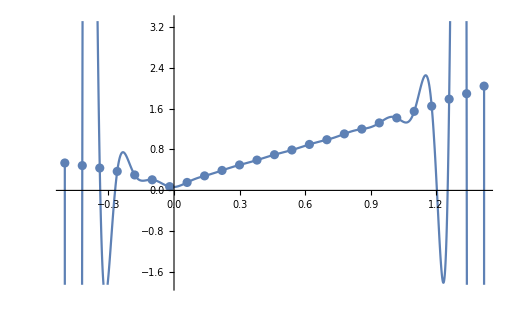

```mathematica
gr1:=Plot[inpln,{x,-0.5,1.42}];
gr2:=ListPlot[data];
Show[{gr1,gr2}]
```

```mathematica
datatemp={};
For[i=1, i<26, i+=2,
datatemp=Append[datatemp,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[datatemp]
```

(-0.5 | 0.535916
-0.34 | 0.437118
-0.18 | 0.301733
-0.02 | 0.073557
0.14 | 0.283913
0.3 | 0.497748
0.46 | 0.69812
0.62 | 0.898493
0.78 | 1.10445
0.94 | 1.31926
1.1 | 1.54526
1.26 | 1.78436
1.42 | 2.03825)

```mathematica
inpln1:=InterpolatingPolynomial[datatemp,x]
Collect[inpln1,x]
```

0.0883836+0.900074 x+7.29475 x^2-31.9226 x^3+15.109 x^4+230.893 x^5-590.834 x^6+208.357 x^7+1283.89 x^8-2456.59 x^9+2017.52 x^10-815.908 x^11+132.599 x^12

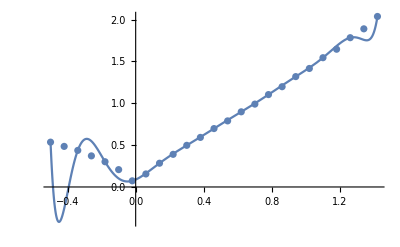

```mathematica
gr3:=Plot[inpln1,{x,-0.5,1.42}];
gr2:=ListPlot[data];
Show[{gr3,gr2}]
```

```mathematica
datatemp2={};
For[i=1, i<26, i+=3,
datatemp2=Append[datatemp2,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[datatemp2]
```

(-0.5 | 0.535916
-0.26 | 0.371678
-0.02 | 0.073557
0.22 | 0.390199
0.46 | 0.69812
0.7 | 0.990582
0.94 | 1.31926
1.18 | 1.64652
1.42 | 2.03825)

```mathematica
inpln2:=InterpolatingPolynomial[datatemp2,x]
Collect[inpln2,x]
```

0.08849+0.847463 x+4.78533 x^2-12.7153 x^3+3.11932 x^4+32.7907 x^5-52.0479 x^6+31.3522 x^7-6.82225 x^8

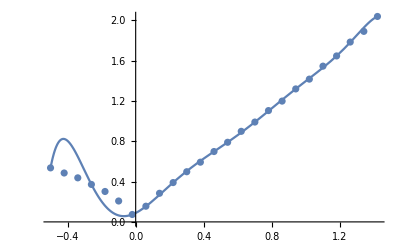

```mathematica
gr4:=Plot[inpln2,{x,-0.5,1.42}];
gr2:=ListPlot[data];
Show[{gr4,gr2}]
```

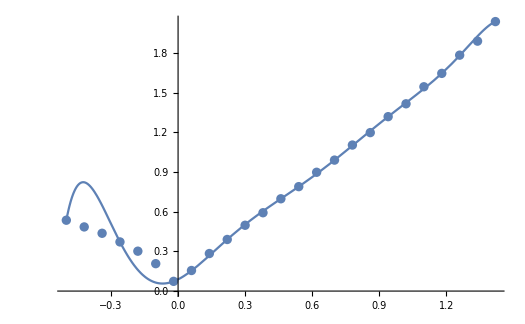

```mathematica
datatemp333={};
For[i=1, i<26, i+=5,
datatemp333=Append[datatemp333,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[datatemp333]
```

(-0.5 | 0.535916
-0.1 | 0.207338
0.3 | 0.497748
0.7 | 0.990582
1.1 | 1.54526)

```mathematica
inpln3:=InterpolatingPolynomial[datatemp333,x]
Collect[inpln3,x]
```

0.242899+0.51432 x+1.45617 x^2-1.26448 x^3+0.449193 x^4

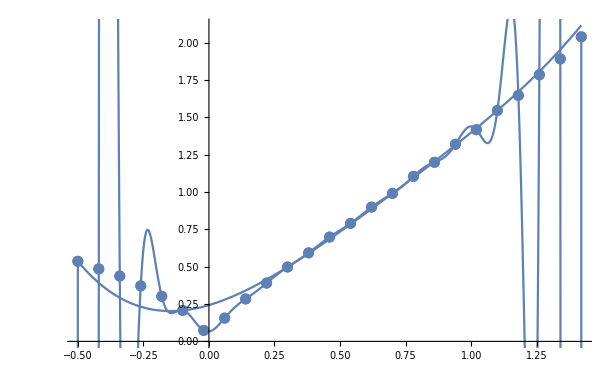

```mathematica
gr5:=Plot[inpln3,{x,-0.5,1.42}];
gr2:=ListPlot[data];
Show[{gr5,gr2,gr1,gr2}]
```

InterpolatingFunction[…]

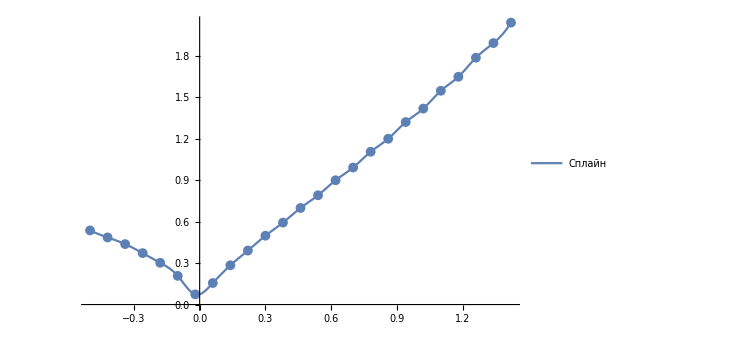

```mathematica
splain1=Interpolation[data,Method->"Spline"]
gr6 = Plot[{splain1[x]},{x,-0.5, 1.42},PlotLegends->{"Сплайн"}];
gr7=ListPlot[data];
Show[{gr6,gr7}]
```